{{2,1.60867},{3,-3.30414},{1+Log[6]/Log[2],-4.21965},{4,-2.48835},{1+Log[10]/Log[2],-1.4166},{1+Log[12]/Log[2],-1.4166},{1+Log[14]/Log[2],-1.27297}}

{{2,1.60867},{3,-3.30414},{1+Log[6]/Log[2],-4.21965},{4,-2.48835},{1+Log[10]/Log[2],-1.4166},{1+Log[12]/Log[2],-1.4166},{1+Log[14]/Log[2],-1.27297}}

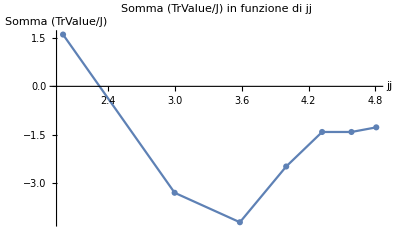

```mathematica
(*Definizione della directory e del formato dei file*)directory="C:\\Users\\meleg\\OneDrive\\Desktop\\Mathematica\\results_TrAmu_complete";
files=Table[FileNameJoin[{directory,"results_TrAmu_j="<>ToString[jj]<>".txt"}],{jj,2,14,2}];

(*Funzione per calcolare la somma richiesta per ogni jj*)
calcolaSomma[jj_]:=Module[{file,data,ultimiTre,somma},(*Costruisce il nome del file*)file=FileNameJoin[{directory,"results_TrAmu_j="<>ToString[jj]<>".txt"}];

(*Importa i dati dal file per jj*)
data=Import[file,"Table"];

(*Verifica se l'importazione ha avuto successo e se ci sono almeno 3 righe di dati*)
If[Head[data]===List&&Length[data]>=3,
(*Estrai gli ultimi tre valori di J e TrValue*)
ultimiTre=Take[data,-3];
(*Calcola la somma TrValue/J per gli ultimi tre valori*)
somma=Plus@@(ultimiTre[[All,2]]/ultimiTre[[All,1]]);
(*Restituisci la somma*)
somma,
Null
]
];

(*Calcolo della somma per ciascun jj*)
resultFunction=Table[{Log2[jj]+1,calcolaSomma[jj]},{jj,2,14,2}];

Print[resultFunction]

(*Rimuove eventuali risultati Null*)
resultFunction=DeleteCases[resultFunction,{_,Null}]

(*Plot della somma calcolata in funzione di jj*)
ListLinePlot[resultFunction,PlotMarkers->Automatic,AxesLabel->{"jj","Somma (TrValue/J)"},PlotLabel->"Somma (TrValue/J) in funzione di jj"]
```

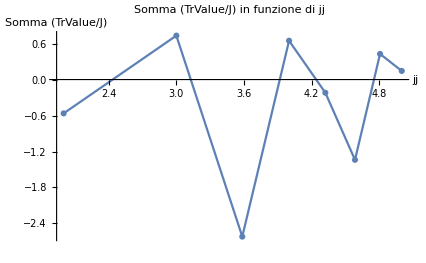

```mathematica
(*Funzione per calcolare i valori di timing per ogni jj*)calcolaTiming[jj_]:=Module[{file,data,timingValue},(*Costruisce il nome del file*)file=FileNameJoin[{directory,"results_TrAmu_j="<>ToString[jj]<>".txt"}];
(*Importa i dati dal file per jj*)data=Import[file,"Table"];
(*Verifica se l'importazione ha avuto successo*)If[Head[data]===List,(*Estrai il valore di Timing*)timingValue=data[[2,2]];
(*Restituisci il valore di Timing*)timingValue,Null]];

(*Calcolo del timing per ciascun jj*)
timingFunction=Table[{jj,calcolaTiming[jj]},{jj,2,14,2}];

(*Rimuove eventuali risultati Null*)
timingFunction=DeleteCases[timingFunction,{_,Null}];

(*Plot del timing in funzione di jj*)
ListLinePlot[timingFunction,PlotMarkers->Automatic,AxesLabel->{"j","Timing"},PlotLabel->"Timing in funzione di j"]
```